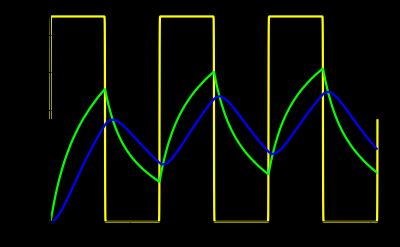

```mathematica
ClearAll["Global*`"];

(* data součástek *)
R1 = 10 * 10^3;
R2 = R1;
R3 = 1 * 10^6;

C1 = 33 * 10^-9;
C2 = 22 * 10^-9;

amplituda = 3.3;
frekvence = 917;

(* Pozor, "uz" musíme zadefinovat jako funkci !!! *)
uz[t_] := amplituda * (1 + Tanh[100 * Sin[2 * π * frekvence * t]]) / 2;

rovnice = {
0 == iU[t] + iR1[t],
iR1[t] == iC1[t] + iR2[t],
iR2[t] == iC2[t] + iR3[t],

u1[t] == uz[t],
u1[t] - u2[t] == R1 * iR1[t],
u2[t] - u3[t] == R2 * iR2[t],
u3[t] == R3 * iR3[t],

iC1[t] == C1 * u2'[t],
iC2[t] == C2 * u3'[t],

u2[0] == 0,
u3[0] == 0
};

tmax = 3/frekvence; (* vykreslujeme 3 periody *)

(* Nyní soustavu rovnic vyřešíme - následující řádky jsou Copy-Paste *)

nezname = Union[Cases[rovnice, _Symbol[t], {0, Infinity}]];
reseni = NDSolve[rovnice, nezname, {t, 0, tmax}, StartingStepSize-> 10^-9];

(* Vykreslení grafu - pozor na parametry *)
Plot[{u1[t] /. reseni[[1]], u2[t] /. reseni[[1]], u3[t] /. reseni[[1]]}, {t, 0, tmax}, PlotStyle -> {Yellow, Green, Blue}, Background -> Black]
```